## Displaying rings graphically

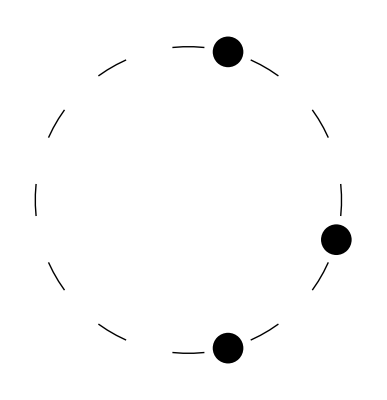

```mathematica
circle12[centre_:{0,0},radius_:1] := Circle[centre,radius, #]&/@Table[π/6{(n + 1 - 0.2),(n + 1 + 0.2)},{n,1,12}]
ringFromNoteList[l_]:= Graphics[{Disk[#,0.1]&/@ CirclePoints[12][[l]],circle12[]}]
ringFromNoteList[{1,3,6}]
```

## Converting between lists of notes and lists of intervals

```mathematica
noteListToIntervalList[l_]:= Table[Mod[l[[1+Mod[n,Length[l]]]]-l[[n]],12],{n,1,Length[l]}]
noteListToIntervalList[{1,3,6}]
```

{2,3,7}

```mathematica
intervalListToNoteList[l_]:= Join[{1},1+Table[Total[l[[1;;n]]],{n,1,Length[l]-1}]]
intervalListToNoteList[{2,3,7}]
```

{1,3,6}

```mathematica
ringFromIntervalList[l_]:=ringFromNoteList[intervalListToNoteList[l]]
ringFromIntervalList[{2,3,7}]
```

-Graphics-

## Converting between note lists, interval lists and binary lists

```mathematica
binaryListToNoteList[l_]:=Module[{output={},i,j=0},
	If[ContainsNone[l,{1}],Return[{}]];
	For[i=FirstPosition[l,1][[1]],i<=Length[l],i++,
		If[l[[i]]==1,AppendTo[output,i]]
	];
	output
]
binaryListToNoteList[{1,0,1,0,0,1}]
```

{1,3,6}

```mathematica
noteListToBinaryList[l_]:=Table[If[ContainsAny[l,{n}],1,0],{n,1,12}]
noteListToBinaryList[{1,3,6}]

intervalListToBinaryList[il_]:=noteListToBinaryList[intervalListToNoteList[il]]
binaryListToIntervalList[bl_]:= noteListToIntervalList[binaryListToNoteList[bl]]
```

{1,0,1,0,0,1,0,0,0,0,0,0}

```mathematica
ringFromBinaryList[l_]:=ringFromNoteList[binaryListToNoteList[l]]
ringFromBinaryList[{1,0,1,0,0,1,0,0,0,0,0,0}]
```

-Graphics-

## Comparing rings to see if they are isomorphic (equivalent structures)

```mathematica
blIsomorphic[bl1_,bl2_]:= ContainsAny[(bl1 == RotateRight[bl2,#])& /@ Range[12],{True}]
nlIsomorphic[nl1_,nl2_]:= blEquals[noteListToBinaryList[nl1],noteListToBinaryList[nl2]]
ilIsomorphic[il1_,il2_]:= nlEquals[intervalListToNoteList[il1],intervalListToNoteList[il2]]
nl1 = {1,3,6};
nl2 = {2,4,7};
nl3 = {2,4,7,8};

nlIsomorphic[nl1,nl2]
nlIsomorphic[nl2,nl3]
```

blEquals[{1,0,1,0,0,1,0,0,0,0,0,0},{0,1,0,1,0,0,1,0,0,0,0,0}]

blEquals[{0,1,0,1,0,0,1,0,0,0,0,0},{0,1,0,1,0,0,1,1,0,0,0,0}]

## Rotating Rings

```mathematica
blRotateRight[bl_,amount_]:=RotateRight[bl,amount]
bl1 = noteListToBinaryList[{1,3,6}]
blRotateRight[bl1,6]

nlRotateRight[nl_,amount_]:=binaryListToNoteList[blRotateRight[noteListToBinaryList[nl],amount]]
nlRotateRight[{1,3,6},3]

(* rotation has a totally different meaning for the interval lists, because they lack a fixed point of reference *)
ilRotateRight[il_,amount_]:= RotateRight[il,amount]
il1 = noteListToIntervalList[{1,3,6}]
ilRotateRight[il1,2]
```

{1,0,1,0,0,1,0,0,0,0,0,0}

{0,0,0,0,0,0,1,0,1,0,0,1}

{4,6,9}

{2,3,7}

{3,7,2}

## Explore the set of all possible rings

### Convert from decimal numbers to binary rings

```mathematica
(* print the digits of the number 5, represented in base 2 *)
IntegerDigits[5,2]

(* convert decimal numbers to rings *)
decimalToBinaryList[d_]:= Module[{},
	(* make sure the number is not too big *)
	Assert[d < 2^12];
	(* convert to binary list and pad zeros on the right side to get a list of length 12 *)
	PadRight[IntegerDigits[d,2],12]
]

(* print the graphic representation of a ring, given its decimal number representation *)
ringFromDecimalNumber[n_]:=ringFromBinaryList[decimalToBinaryList[n]]

decimalToBinaryList[3]
```

{1,0,1}

{1,1,0,0,0,0,0,0,0,0,0,0}

### Explore the space, up to isomorphism

The total number of all possible binary lists is 2^12 - 1, but many of them are isomorphic to eachother. We count the number of unique rings.

```mathematica
decimalIsomorphic[d1_,d2_]:= blIsomorphic[decimalToBinaryList[d1],decimalToBinaryList[d2]]

(* this generates a complete list of all 2^12 -1 rings *)
completeSet = Range[0,2^12 - 1];

(* this is the set of all unique rings, with isomorphic duplicates removed *)
uniqueSet = DeleteDuplicates[completeSet,decimalIsomorphic[#1,#2]&];

(* the total number of unique rings is 352 *)
Length[uniqueSet]
```

352

We print the complete set of unique rings

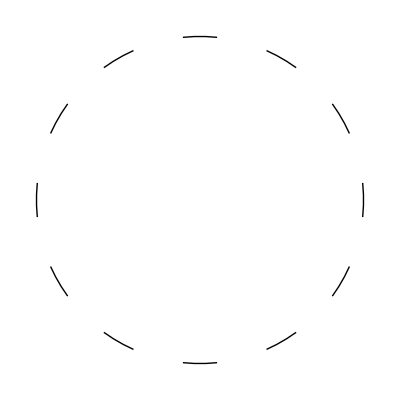
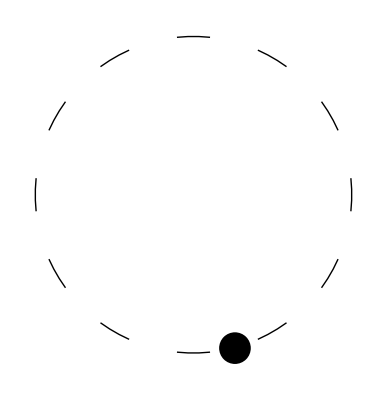
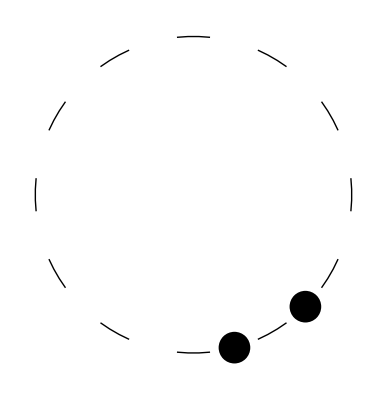
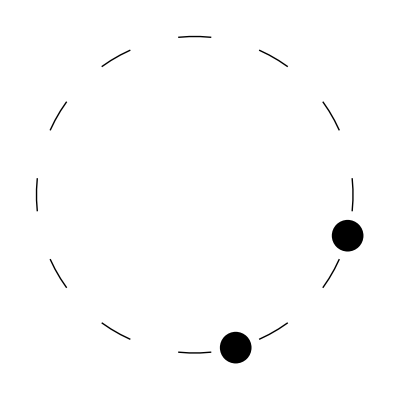
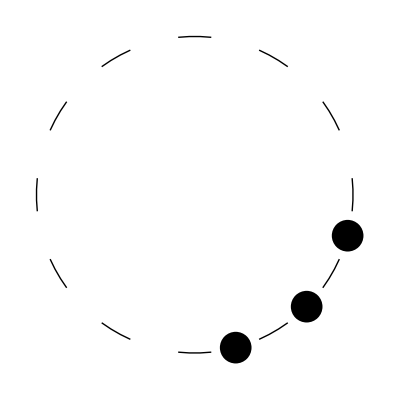
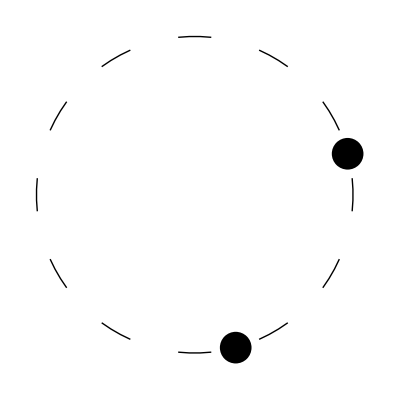
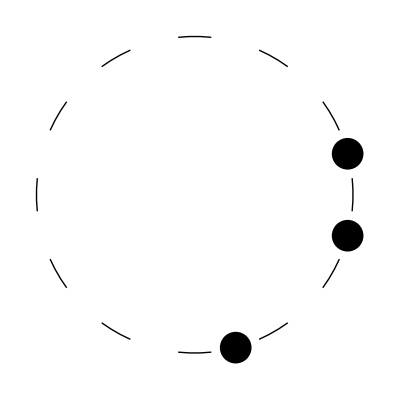
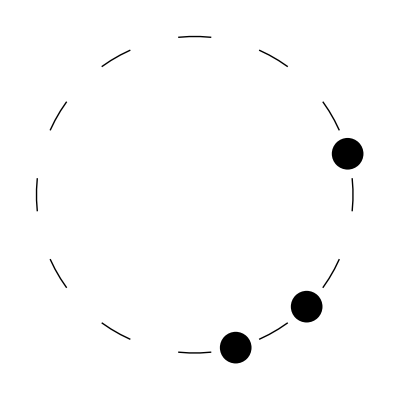
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ringFromDecimalNumber[#]& /@ uniqueSet
```